1.41421

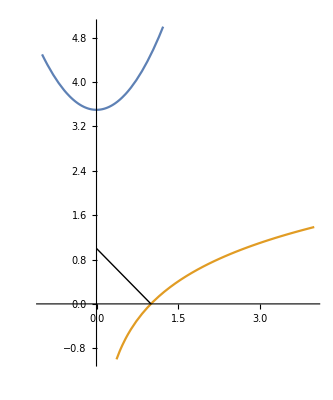

```mathematica
r1=ImplicitRegion[y==E^x,{x,y}];
r2=ImplicitRegion[y==Log[x],{x,y}];

dist=FixedPoint[Apply@Function[{r1,r2,p1,p2},{r2,r1,p2,RegionNearest[r1,Rationalize[N[p2],0]]}],{r1,r2,{1.,1.},{1.1,1.1}},50,(*max iterations*)SameTest->Function[{l1,l2},Norm[l1[[3;;]]-Reverse@l2[[3;;]],"Frobenius"]/Norm[l2[[3;;]],"Frobenius"]<1*^-8]][[3;;]];

EuclideanDistance@@dist//N
(*3.35325*)

Plot[{x^2+7/2,Log[x]},{x,-1,4},Epilog->{Line@dist},AspectRatio->Automatic,PlotRange->{-1,5}]
```

```mathematica
ℛ1=ImplicitRegion[y==E^x,{x,y}];
ℛ2=ImplicitRegion[y==Log[x],{x,y}];
p={p1,p2};
q={q1,q2};
Minimize[EuclideanDistance[p,q],{p∈ℛ1,q∈ℛ2}]//FullSimplify
```

{-1+3/(√2),{p1→1/(√2),p2→1/(√2),q1→3/2,q2→3/2}}

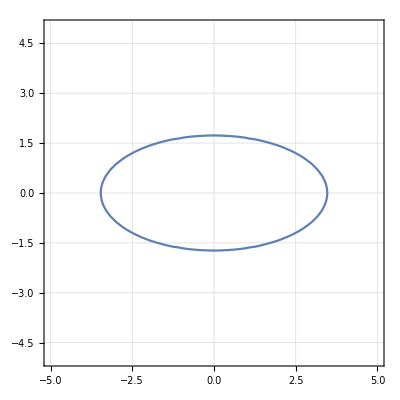
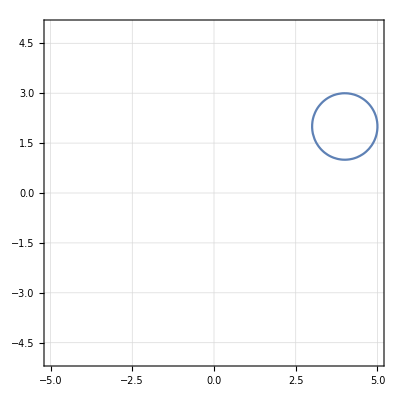

```mathematica
f[x_,y_]:=x^2/4+y^2==3;
g[x_,y_]:=(x-4)^2+(y-2)^2==1;
c1=ContourPlot[Evaluate@f[x,y],{x,-5,5},{y,-5,5},GridLines->Automatic];
c2=ContourPlot[Evaluate@g[x,y],{x,-5,5},{y,-5,5},GridLines->Automatic];
Overlay[{c1,c2}]
```

```mathematica
ℛ1=ImplicitRegion[Evaluate@f[x,y],{x,y}];
ℛ2=ImplicitRegion[Evaluate@g[x,y],{x,y}];
p={p1,p2};
q={q1,q2};
Minimize[EuclideanDistance[p,q],{p∈ℛ1,q∈ℛ2}]//FullSimplify
```

{Root0.512Root[54196-93640 #1-29296 #1^2+12772 #1^3-2603 #1^4-3276 #1^5-378 #1^6+72 #1^7+9 #1^8&,3]0.5118841040742709,{p1→Root3.01Root[{2937206416-11943901632 #1+2968051400 #1^2-665110464 #1^3+127065217 #1^4-11130804 #1^5+567774 #1^6-11988 #1^7+81 #1^8&,«1»&,48664576+6520832 #1+288768 #1^2+8192 #1^3+256 #1^4-78577664 #2-8028160 #1 #2-311296 #1^2 #2-8192 #1^3 #2+49307648 #2^2+3833856 #1 #2^2+112640 #1^2 #2^2-15007744 #2^3-753664 #1 #2^3+1970176 #2^4+13041664 #2 #3+1155072 #1 #2 #3+«48»+864 #1^2 #3^4-467968 #2 #3^4-19968 #1 #2 #3^4+60800 #2^2 #3^4-8448 #1 #2^2 #3^4+79872 #2^3 #3^4+2304 #2^4 #3^4+44544 #2 #3^5+3456 #1 #2 #3^5-39936 #2^2 #3^5-4608 #2^3 #3^5-6624 #3^6-432 #1 #3^6+5760 #2 #3^6+3168 #2^2 #3^6-864 #2 #3^7+81 #3^8&},{1,2,2}]3.005828035538331,p2→Root0.861Root[{2937206416-11943901632 #1+2968051400 #1^2-665110464 #1^3+127065217 #1^4-11130804 #1^5+567774 #1^6-11988 #1^7+81 #1^8&,2894356990320+471413094848 #1+37566945592 #1^2+3588484544 #1^3+19440399 #1^4+16865844 #1^5-376182 #1^6+«75»+2625470400 #1 #2^8+51564744 #1^2 #2^8+295056 #1^3 #2^8+81 #1^4 #2^8-5493616896 #2^9-193209984 #1 #2^9-1954368 #1^2 #2^9-2592 #1^3 #2^9+398610144 #2^10+7575552 #1 #2^10+27864 #1^2 #2^10-17286912 #2^11-114048 #1 #2^11+343440 #2^12&,48664576+6520832 #1+288768 #1^2+8192 #1^3+«87»+5760 #2 #3^6+3168 #2^2 #3^6-864 #2 #3^7+81 #3^8&,-12+#3^2+4 #4^2&},{1,2,2,2}]0.8609584514905144,q1→Root3.34Root[{2937206416-11943901632 #1+2968051400 #1^2-665110464 #1^3+127065217 #1^4-11130804 #1^5+567774 #1^6-11988 #1^7+81 #1^8&,2894356990320+471413094848 #1+37566945592 #1^2+3588484544 #1^3+19440399 #1^4+16865844 #1^5-376182 #1^6+«75»+2625470400 #1 #2^8+51564744 #1^2 #2^8+295056 #1^3 #2^8+81 #1^4 #2^8-5493616896 #2^9-193209984 #1 #2^9-1954368 #1^2 #2^9-2592 #1^3 #2^9+398610144 #2^10+7575552 #1 #2^10+27864 #1^2 #2^10-17286912 #2^11-114048 #1 #2^11+343440 #2^12&},{1,2}]3.3424284561346043,q2→Root1.25Root[{2937206416-11943901632 #1+2968051400 #1^2-665110464 #1^3+127065217 #1^4-11130804 #1^5+567774 #1^6-11988 #1^7+81 #1^8&,2894356990320+471413094848 #1+37566945592 #1^2+3588484544 #1^3+19440399 #1^4+16865844 #1^5-376182 #1^6+«75»+2625470400 #1 #2^8+51564744 #1^2 #2^8+295056 #1^3 #2^8+81 #1^4 #2^8-5493616896 #2^9-193209984 #1 #2^9-1954368 #1^2 #2^9-2592 #1^3 #2^9+398610144 #2^10+7575552 #1 #2^10+27864 #1^2 #2^10-17286912 #2^11-114048 #1 #2^11+343440 #2^12&,19-8 #2+#2^2-4 #3+#3^2&},{1,2,1}]1.2466078944543686}}

```mathematica
Out[64]//N
```

{0.511884,{p1→3.00583,p2→0.860958,q1→3.34243,q2→1.24661}}